# Graphene Nanoribbons

This notebook contains code for calculating and plotting the band structures of armchair and zigzag graphene nanoribbons in a magnetic field.  The extensive examples section shows how to use the code to reproduce figures from the recent literature.  The final section explores the scaling of Landau level energies with the level index.

This code is provided under the (very liberal) terms of the MIT license, a copy of which you ought to have received along with this file.

## Function definitions

This section contains the function definitions and their documentation.

First, let’s define the necessary constants:

```mathematica
echarge=1.6*10^-19;
hbar=1.05457*10^-34;
graphenebond=1.42*10^-10;
```

### showRibbon

Throughout this notebook, the width of nanoribbons is measured in unit cells.  But what does an “armchair nanoribbon, width 5” actually look like?  To avoid any ambiguity, the function showRibbon can be used to draw a section of a nanoribbon of specified type and width.  showRibbon calls one of two other functions, cella or cellz; these plot the unit cells of armchair and zigzag nanoribbons, respectively.  The lattice vectors I use for the armchair and the zigzag are (unit1a, unit2a) and (unit1z, unit2z).

Roughly speaking, the unit cell used in this notebook is such that the width of the nanoribbon is the number of vertical chains of carbon atoms that make it up.  For some examples that make this notion clearer, see the next section.

```mathematica
Options[showRibbon]={Type->"zigzag"};

showRibbon[width_,OptionsPattern[]]:=Module[{cell},
cell=Switch[OptionValue@Type,"armchair",cella,"zigzag",cellz];
Graphics[Table[cell[i,j],{i,1,width+1},{j,1,width}]]];

cella[i_,j_]:=Point[{unit1a*i+unit2a*j,{0,1}+unit1a*i+unit2a*j}];
unit1a={0,3};unit2a={(√3)/2,3/2};
cellz[i_,j_]:=Point[{unit1z*i+unit2z*j,{-1/2,(√3)/2}+unit1z*i+unit2z*j}];
unit1z={0,√3}; unit2z={3/2,(√3)/2};
```

### spectrumPlot

The function spectrumPlot plots the bandstructure of a nanoribbon.  It takes as input the nanoribbon width (in unit cells) and magnetic field value (in Tesla); it can also be passed a variety of options.  In addition to any option accepted by ListPlot (particularly useful are Ticks and PlotRange), the function can handle the following:

Type, which can be set to ”zigzag” or ”armchair” (the double quotes are necessary).

tprime  is the value of the next-nearest hopping, measured in units of the nearest-neighbour hopping, t.  The default value is 0.

Levels is the number of bands to be plotted; it is passed as the second argument to Eigenvalues, the built-in function that diagonalizes the tight-binding matrix. Setting Levels → -8, for instance, will plot the 8 bands with the lowest absolute values of the energy.  Note the minus sign: setting Levels → 8 gives the 8 bands with the highest absolute values of the energy.  Note also that, for the defaul case of t'=0, the nanoribbon bands come in pairs, degenerate up to a minus sign (and numerical inaccuracies): in this case, picking an odd value for Levels will result in an illegible plot, as the plotting function tries to join pieces of the positive- and negative-energy bands into one curve.  Hence, pick even values for Levels.

SpectrumLabel determines whether a label should be placed above the plot.  If set to True, the plot is labelled with the ribbon type and width, the B field applied, and the value of t'.  If set to False, no label is generated.

The width of the Brillouin zone is defined to be 2π for all ribbon types.  This convention puts me in conformance with the literature, but it obscures the fact that the actual BZ width depends on the ribbon type.  (The BZ width is (2π)/(3a)for an armchair nanoribbon and (2π)/(√3 a)for a zigzag nanoribbon, where a is the graphene bond length.)

```mathematica
spectrumPlotDefaults=Options[spectrumPlot]={PlotRange->Full,Levels->All,SpectrumLabel->True,Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},Type->"zigzag",PlotStyle->Red,AxesLabel->{"k×'a'","E/t"},DataRange->{0,2π},Joined->True,tprime->0};
spectrumPlot[width_,B_,opts:OptionsPattern[]]:=Module[{mat,label},
mat=Switch[OptionValue@Type,"armchair",armchairBMatrix[width,B,OptionValue@tprime],"zigzag",zigzagBMatrix[width,B,OptionValue@tprime],_,Message[spectrumPlot::type,OptionValue@Type];IdentityMatrix[width]] ;

label=OptionValue@Type<>" nanoribbon, width "<>ToString[width]<>" in B = "<>ToString[B]<>" T (t' = "<>ToString[OptionValue@tprime]<>")";

ListPlot[Table[Sort[Eigenvalues[N[Chop[mat]],OptionValue@Levels]],{k,0,2π,0.01}]ᵀ,PlotLabel->If[OptionValue@SpectrumLabel,label,None],FilterRules[{opts},Options[ListPlot]],
FilterRules[FilterRules[spectrumPlotDefaults,Options[ListPlot]],Except[{opts}]]]
];
spectrumPlot::type="The requested type `1` is not 'zigzag' or 'armchair'.";
```

### armchairBMatrix, zigzagBMatrix

The heart of this notebook’s code are the twin functions used to construct the tight-binding matrices for graphene nanoribbons.  Their inputs are the width of the nanoribbon (in unit cells) and the strength of the magnetic field (in Tesla); the value of the next-nearest hopping t', expressed as a fraction of the nearest-neighbour hopping t, can be passed as an optional third argument.  The functions return tight-binding matrices in the (a_1,b_1,a_2,b_2,...,a_m,b_m) basis, where m is the width of the nanoribbon and a_j (b_j) represents the annihilation of an electron at the A (B) sublattice site.  The matrices are functions of a parameter k, which is the crystal momentum measured in units of the lattice constant.  (The lattice constant is 3a for armchair and √3 a for zigzag, where a is the graphene bondlength.)  The eigenvalues of these matrices are the band energies.

```mathematica
armchairBMatrix[width_,B_,tprime_:0]:=Module[{e,tzero,tplus,fullMatrix,diagonalBlock,aboveDiagonalBlock,Φ,primeAboveDiagonalBlock,primeAAboveDiagonalBlock},
e=Exp[I*k];
tzero[x_]:=Exp[-I*(echarge*B*graphenebond^2)/hbar*(√3)/2 x];
tplus[x_]:=Exp[I*(echarge*B*graphenebond^2)/hbar*(√3)/4(x+1/2)];
fullMatrix=Table[0,{i,1,2*width},{j,1,2*width}];
diagonalBlock[j_]:={{0,tzero[j]},{0,0}};
aboveDiagonalBlock[j_]:={{0,tplus[j]*e},{Conjugate[tplus[j]],0}};
For[i=0,i≤width-1,i++,fullMatrix[[1+2i;;2+2i,1+2i;;2+2i]]=diagonalBlock[i+1];];
If[width≥2,
For[i=0,i≤width-2,i++,
j=i+1;
fullMatrix[[1+2i;;2+2i,1+2j;;2+2j]]=aboveDiagonalBlock[i+1]];];

(* Next-nearest neighbour hoppings *)
If[tprime≠0,
Φ=(I×echarge×B×graphenebond^2)/hbar*(3 √3)/8;
primeAboveDiagonalBlock[j_]:=tprime*(Exp[(2j+1)Φ+I*k]+Exp[-(2j+1)Φ])*{{1,0},{0,1}};
primeAAboveDiagonalBlock:=tprime*Exp[I*k]*{{1,0},{0,1}};
If[width≥2,
For[i=0,i≤width-2,i++,
j=i+1;
fullMatrix[[1+2i;;2+2i,1+2j;;2+2j]]+=primeAboveDiagonalBlock[i+1]];];
If[width≥3,
For[i=0,i≤width-3,i++,
j=i+2;
fullMatrix[[1+2i;;2+2i,1+2j;;2+2j]]+=primeAAboveDiagonalBlock];];
];

fullMatrix=FullSimplify[fullMatrix+ConjugateTranspose[fullMatrix],Assumptions->k∈Reals];
Return[-fullMatrix];];

zigzagBMatrix[width_,B_,tprime_:0]:=Module[{e,m,Φ,fullMatrix,diagonalBlock,aboveDiagonalBlock,primeDiagonalBlock,primeAboveDiagonalBlock},
e=Exp[I*k];
m[j_]:=Exp[I*(echarge*B)/hbar*(√3 graphenebond^2)/4*(3j+1/2)];
fullMatrix=Table[0,{i,1,2*width},{j,1,2*width}];
diagonalBlock[j_]:={{0,m[j]+e*Conjugate[m[j]]},{0,0}};
aboveDiagonalBlock={{0,0},{1,0}};
For[i=0,i≤width-1,i++,fullMatrix[[1+2i;;2+2i,1+2i;;2+2i]]=diagonalBlock[i+1];];
If[width≥2,
For[i=0,i≤width-2,i++,
j=i+1;
fullMatrix[[1+2i;;2+2i,1+2j;;2+2j]]=aboveDiagonalBlock];];

(* Next-nearest neighbour hoppings *)
If[tprime≠0,
Φ=(I×echarge×B×graphenebond^2)/hbar*(3 √3)/8;
primeDiagonalBlock[j_]:=tprime*{{Exp[-4j*Φ-I*k],0},{0,Exp[-(4j-4/3)*Φ-I*k]}};
primeAboveDiagonalBlock[j_]:=tprime*{{Exp[(2j+1)*Φ]+Exp[-(2j+1)*Φ+I*k],0},{0,Exp[(2j+5/3)*Φ]+Exp[-(2j+5/3)*Φ+I*k]}};
For[i=0,i≤width-1,i++,fullMatrix[[1+2i;;2+2i,1+2i;;2+2i]]+=primeDiagonalBlock[i+1];];
If[width≥2,
For[i=0,i≤width-2,i++,
j=i+1;
fullMatrix[[1+2i;;2+2i,1+2j;;2+2j]]+=primeAboveDiagonalBlock[i+1]];];
];

fullMatrix=FullSimplify[fullMatrix+ConjugateTranspose[fullMatrix],Assumptions->k∈Reals];
Return[-fullMatrix];];
```

## Some examples

### 1D chain of atoms and dimer

As a sanity check, let’s investigate the 1D chain of atoms.  The band structure produced by the program is shown below:

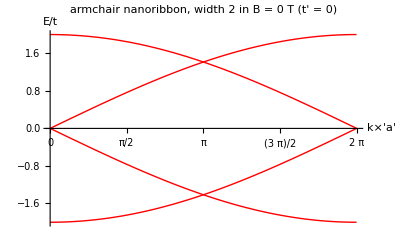

```mathematica
spectrumPlot[2,0,Type->"armchair"]
```

The width argument of spectrumPlot had to be set to 2 because of the shape of our unit cells and lattice vectors.  Setting the width to 1 would have produced a chain of isolated dimers.  Compare the two ribbons below.  The one on the left has width 2, while the one on the right has width 1:

```mathematica
GraphicsRow[{showRibbon[2,Type->"armchair"],showRibbon[1,Type->"armchair"]}]
```

-Graphics-

The expected band structure of the 1D chain is 2cos kx.  The result we obtained above is equivalent, if one keeps in mind that the BZ was folded on itself 4 times because we used a unit cell with four atoms (rather than one).

Incidentally, below is the “band structure” of a dimer.  As expected, the dimer has a discrete spectrum with only two energy levels:

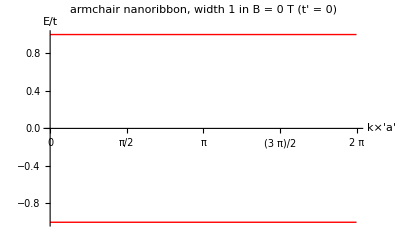

```mathematica
spectrumPlot[1,0,Type->"armchair"]
```

### Narrow zigzag nanoribbon

The figures below reproduce the left panels of Figure 4 in Peres, Castro Neto and Guinea, “Conductance Quantization in Mesoscopic Graphene” (Physical Review B, 2006):

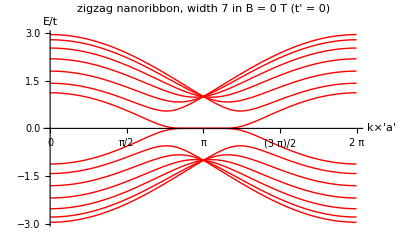

```mathematica
spectrumPlot[7,0,Type->"zigzag"]
```

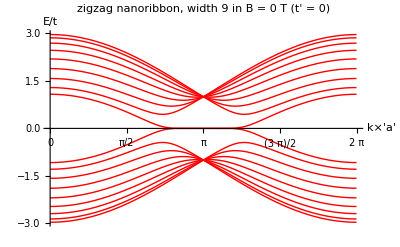

```mathematica
spectrumPlot[9,0,Type->"zigzag"]
```

This is what the ribbons look like in real space:

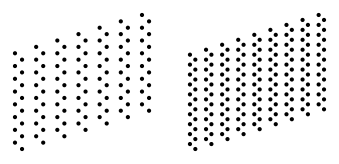

```mathematica
GraphicsRow[{showRibbon[7,Type->"zigzag"],showRibbon[9,Type->"zigzag"]}]
```

### Nakada nanoribbon

The nanoribbon spectrum below was plotted as Figure 4(d) by Nakada, Fujita, Dresselhaus and Dresselhaus in their 1996 Phys Rev B article “Edge state in graphene nanoribbons: Nanometer size effect and edge shape dependence”.

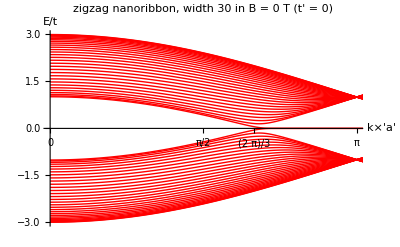

```mathematica
spectrumPlot[30,0,Type->"zigzag",PlotRange->{{0,π},Automatic},Ticks->{{0,π/2,2π/3,π},Automatic}]
```

### Narrow armchair nanoribbon

The figures below reproduce the right panels of Figure 4 in Peres et al. (2006).  Note that, as in the paper cited, the first nanoribbon is gapless at k=0, while the second exhibits a gap.

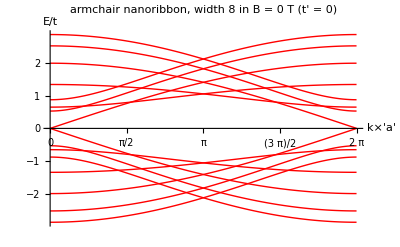

```mathematica
spectrumPlot[8,0,Type->"armchair"]
```

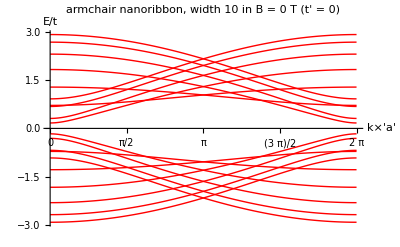

```mathematica
spectrumPlot[10,0,Type->"armchair"]
```

These spectra correspond to the following ribbons:

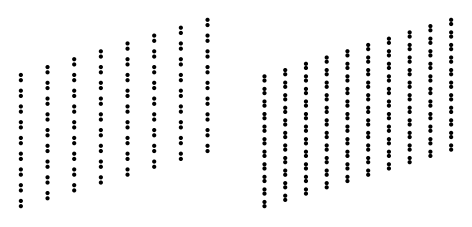

```mathematica
GraphicsRow[{showRibbon[8,Type->"armchair"],showRibbon[10,Type->"armchair"]}]
```

### Broader nanoribbons: Fig 17 of Castro Neto (2009)

The figures below reproduce Figure 17 in Castro Neto, “Electronic Properties of Graphene” (Reviews of Modern Physics, 2009).  Note that only the 14 lowest-energy bands are shown.

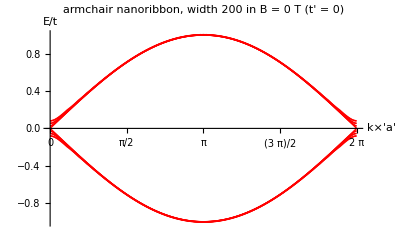

```mathematica
spectrumPlot[200,0,Type->"armchair",Levels->-14]
```

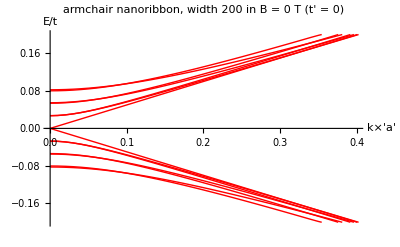

```mathematica
spectrumPlot[200,0,Type->"armchair",Levels->-14,PlotRange->{{0,0.4},{-0.2,0.2}},Ticks->Automatic]
```

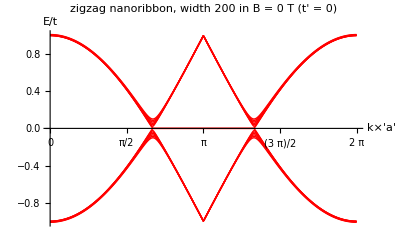

```mathematica
spectrumPlot[200,0,Type->"zigzag",Levels->-14]
```

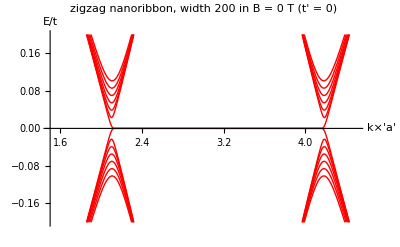

```mathematica
spectrumPlot[200,0,Type->"zigzag",Levels->-14,PlotRange->{{1.5,4.5},{-0.2,0.2}},Ticks->Automatic]
```

### Armchair nanoribbon in B field

The figure below shows the 20 bands closest to E=0 for an armchair nanoribbon in a magnetic field.  Although the field is rather strong, there is no signature of Landau levels; the main consequence of applying the field is breaking the E(k)=E(-k) symmetry of the band structure.  (I suspect this is related to the fact that, in the continuum model of an infinite sheet, the primary effect of a weak magnetic field is a shift in the position of the Dirac point.)  Fields of similar magnitude have a much more dramatic effect on wider nanoribbons, as we will see later in this notebook.

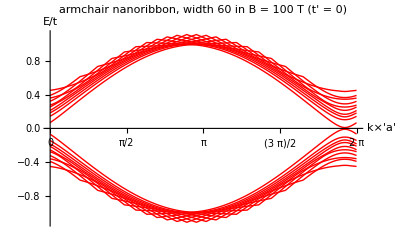

```mathematica
spectrumPlot[60,100,Type->"armchair",Levels->-20]
```

### Broad nanoribbons in B field

The plots below reproduce Figure 21 of Castro Neto (2009).  Note that the low-energy bands now have horizontal segments reminiscent of Landau Levels.

```mathematica
field=1/701*(hbar*2π)/echarge*1/((3 √3)/2*graphenebond^2);
```

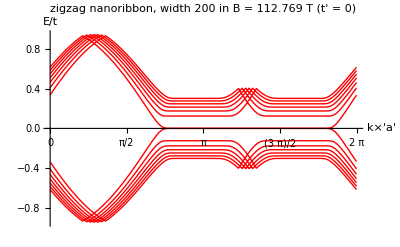

```mathematica
spectrumPlot[200,field,Type->"zigzag",Levels->-14]
```

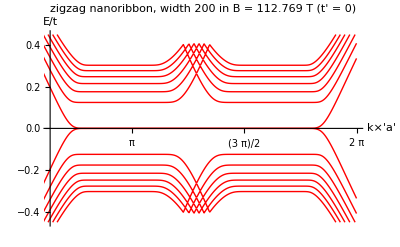

```mathematica
spectrumPlot[200,field,PlotRange->{{2,2π},{-0.45,0.45}},Levels->-14]
```

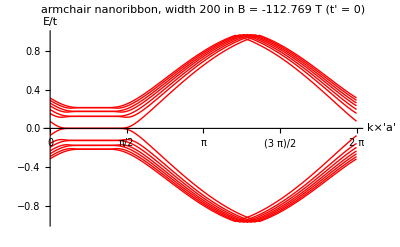

```mathematica
spectrumPlot[200,-field,Levels->-14,Type->"armchair"]
```

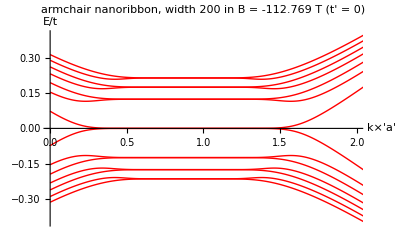

```mathematica
spectrumPlot[200,-field,Levels->-14,Type->"armchair",Ticks->Automatic,PlotRange->{{0,2},{-0.4,0.4}}]
```

### Next-nearest neighbour interactions

The code in this notebook can account for next-nearest neighbour interactions.  The figure below (equivalent to Fig. 5 in Peres (2005)) compares zigzag nanoribbon spectra obtained with and without accounting for next-nearest neighbour hopping terms.  The effect of next-nearest neighbour hopping is dramatic: the E_-(k)=-E_+(k) symmetry of positive- and negative-energy bands is broken, and the zero-mode shifts upwards.

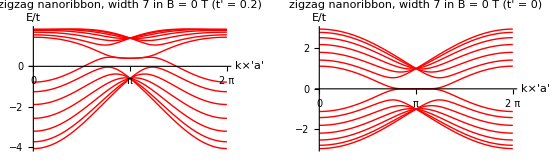

```mathematica
GraphicsRow[{spectrumPlot[7,0,tprime->0.2,Type->"zigzag"],spectrumPlot[7,0,Type->"zigzag"]}]
```

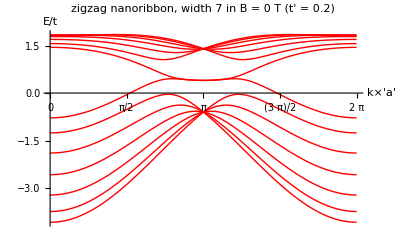

```mathematica
spectrumPlot[7,0,tprime->0.2,Type->"zigzag"]
```

The figure below shows the spectrum of the broad zigzag nanoribbon studied in the previous section, but with t'≠0.

```mathematica
spectrumPlot[200,0,tprime->0.2,Type->"zigzag"]
```

-Graphics-

The details are impossible to make out here, so let’s take a closer look at one of the “cones”:

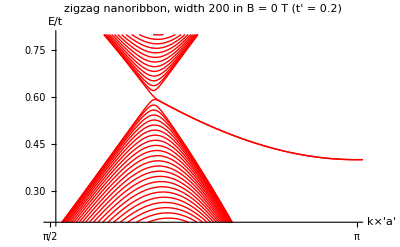

```mathematica
spectrumPlot[200,0,tprime->0.2,Type->"zigzag",PlotRange->{{π/2,π},{0.2,0.8}}]
```

## Scaling of Landau levels

This section of the notebook contains code for studying the √n scaling of the Landau level spacing in nanoribbons.  Specifically, it provides functions for finding, fitting and plotting Landau levels of nanoribbons at specified momentum values.

### Function definitions

#### Legendmaker

The cell below contains functions for creating plot legends.  Courtesy of Stack Exchange: Mathematica. (http://mathematica.stackexchange.com/)

```mathematica
Options[legendMaker]=Join[FilterRules[Options[Framed],Except[{ImageSize,FrameStyle,Background,RoundingRadius,ImageMargins}]],{FrameStyle->None,Background->Directive[Opacity[.7],LightGray],RoundingRadius->10,ImageMargins->0,PlotStyle->Automatic,PlotMarkers->None,"LegendLineWidth"->35,"LegendLineAspectRatio"->.3,"LegendMarkerSize"->8,"LegendGridOptions"->{Alignment->Left,Spacings->{.4,.1}}}];

legendMaker[textLabels_,opts:OptionsPattern[]]:=Module[{f,lineDirectives,markerSymbols,n=Length[textLabels],x},lineDirectives=((PlotStyle/.{opts})/.PlotStyle|Automatic:>Map[ColorData[1],Range[n]])/.None->{None};
markerSymbols=Replace[((PlotMarkers/.{opts})/.Automatic:>(Drop[ListPlot[Transpose[{Range[n]}],PlotMarkers->Automatic][[1,2]][[1]],-1]/.Inset[x_,i__]:>x)[[All,-1]])/.{Graphics[gr__],sc_}:>Graphics[gr,ImageSize->("LegendMarkerSize"/.{opts}/.Options[legendMaker,"LegendMarkerSize"]/.{"LegendMarkerSize"->8})],PlotMarkers|None:>Map[Style["",Opacity[0]]&,textLabels]]/.None|{}->Style["",Opacity[0]];
lineDirectives=PadRight[lineDirectives,n,lineDirectives];
markerSymbols=PadRight[markerSymbols,n,markerSymbols];
f=Grid[MapThread[{Graphics[{#1/.None->{},If[#1==={None}||(PlotStyle/.{opts})===None,{},Line[{{-.1,0},{.1,0}}]],Inset[#2,{0,0},Background->None]},AspectRatio->("LegendLineAspectRatio"/.{opts}/.Options[legendMaker,"LegendLineAspectRatio"]/.{"LegendLineAspectRatio"->.2}),ImageSize->("LegendLineWidth"/.{opts}/.Options[legendMaker,"LegendLineWidth"]/.{"LegendLineWidth"->35}),ImagePadding->{{1,1},{0,0}}],Text[#3,FormatType->TraditionalForm]}&,{lineDirectives,markerSymbols,textLabels}],Sequence@Evaluate[("LegendGridOptions"/.{opts}/.Options[legendMaker,"LegendGridOptions"]/.{"LegendGridOptions"->{Alignment->Left,Spacings->{.4,.1}}})]];
Framed[f,FilterRules[{Sequence[opts,Options[legendMaker]]},FilterRules[Options[Framed],Except[ImageSize]]]]];
```

#### landauLevels

landauLevels returns a list of Landau level indexes and their corresponding energies, given a ribbon type and momentum value.

```mathematica
landauLevels[width_,B_,momentum_,Type_:"zigzag"]:=Module[{mat,x},
mat=Switch[Type,"armchair",armchairBMatrix[width,B],"zigzag",zigzagBMatrix[width,B]];
x=Switch[Type,"armchair",{0,0}~Join~Table[Floor[i],{i,1,(4*width+2)/8,0.25}],"zigzag",Table[Floor[i],{i,0,(2*width-1)/2,0.5}]];Return[{x,Sort[Eigenvalues[N[mat/.k->momentum]],Abs[#1]<Abs[#2]&]}ᵀ];];
```

#### landauScalingFit

The function landauScalingFit fits the model a×√n to the Landau level spectrum using maximum likelihood.  The required arguments are the width of the nanoribbon, the B field applied, and the momentum value at which the Landau levels are to be evaluated.  The output is a NonlinearModelFit object.  The function accepts the following options:

Any options accepted by NonlinearModelFit.

Type: The type of nanoribbon, ”zigzag” or ”armchair”.

FittedLevels: The fit is performed only to a certain number of lowest-lying Landau levels.  That number is equal to the lesser of two quantities, twice fittedLevels or twice ribbon width.  (The number of bands of the nanoribbon is only twice the width, so if fittedLevels exceeds width, all Landau levels will be fit.)

LevelsList: If the Landau levels have already been found, they can be input directly using the levelsList option to avoid needlessly recalculating them.  (For an example of this option’s usage, see the landauScalingPlot function, below).

```mathematica
Options[landauScalingFit]={FittedLevels->50,Type->"zigzag",LevelsList->None};

landauScalingFit[width_,B_,momentum_,opts:OptionsPattern[]]:=Module[{points,lls},
points=Min[OptionValue[FittedLevels]*2,width*2];
lls=Switch[OptionValue@LevelsList,None,landauLevels[width,B,momentum,OptionValue@Type],_,OptionValue@LevelsList];
Return[NonlinearModelFit[Abs[lls][[1;;points]],a*√x,{a},x, FilterRules[{opts}, Options@NonlinearModelFit]]];];
```

#### grapheneLandauScaling

The expected scaling of the Landau levels with index, n, and field strength, B, obtained from the continuum model:

```mathematica
grapheneLandauScaling[n_,B_]:=(3 √2)/2*(graphenebond*√(echarge*Abs[B]*n))/(√hbar);
```

#### landauScalingPlot

A top-level function for exhibiting the √n scaling of the Landau level spectrum of a nanoribbon.  Given the ribbon width, field strength B and momentum value, it produces a plot showing the Landau level spacing, the maximum likelihood fit to the model a √n, and the spacing expected in an infinite graphene sheet.

```mathematica
Options[landauScalingPlot]={FittedLevels->50,Type->"zigzag"};

landauScalingPlot[width_,B_,momentum_,opts:OptionsPattern[]]:=Module[{fit,ω,listplot,expectedplot,labels,lls,points},
lls=landauLevels[width,B,momentum,OptionValue@Type];

points=Min[OptionValue[FittedLevels]*2,width*2];
listplot=ListPlot[Abs[lls][[1;;points]],AxesLabel->{"LL index","E/t"},PlotLabel->StringJoin["LL scaling for ",OptionValue[Type]," nanoribbon of width ",ToString[width]," at k = ",ToString[N[momentum]]]];
fit=landauScalingFit[width,B,momentum,LevelsList->lls,FilterRules[{opts}, Options[landauScalingFit]]];

expectedplot=Plot[{fit[n],grapheneLandauScaling[n,B]},{n,0,points}];
labels={"ML fit","Inifite sheet result"};

Overlay[{Show[listplot,expectedplot],legendMaker[labels]},Alignment->{Right,-0.7}]];
```

### Examples of use

#### Zigzag nanoribbon

A 200-unit-cells wide zigzag nanoribbon in a fairly strong field (B≃100 Tesla) appears to have well-formed Landau levels around k=π:

```mathematica
field=1/701*(hbar*2π)/echarge*1/((3 √3)/2*graphenebond^2);
```

```mathematica
spectrumPlot[200,field,PlotRange->{{2,2π},{-0.45,0.45}},Levels->-14]
```

-Graphics-

The first 50 Landau levels scale as √n, with a prefactor almost identical to that of the infinite sheet:

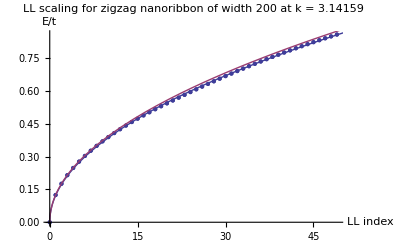
-Graphics--Graphics- | ML fit
-Graphics- | Inifite sheet result

```mathematica
landauScalingPlot[200,field,π,FittedLevels->50,Type->"zigzag"]
```

The two can be compared explicitly:

```mathematica
grapheneLandauScaling[1,field]
```

0.124598

```mathematica
landauScalingFit[200,field,π,Type->"zigzag",FittedLevels->50]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.122233 | 0.0000521109 | 2345.64 | 1.07341×10^-236

The scaling breaks down for high values of n:

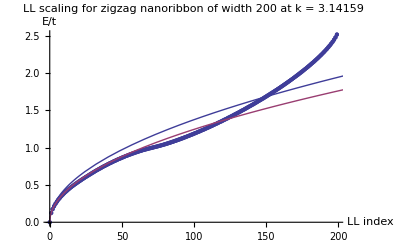
-Graphics--Graphics- | ML fit
-Graphics- | Inifite sheet result

```mathematica
landauScalingPlot[200,field,π,FittedLevels->200,Type->"zigzag"]
```

In the plots above, the positive- and negative-energy Landau levels have been lumped together.  This is justified, as their energies are nearly identically opposite:

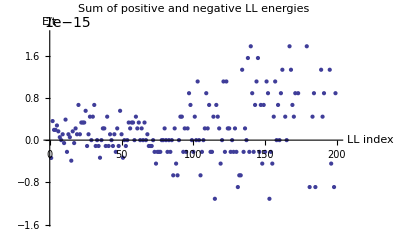

```mathematica
lls=landauLevels[200,field,π,"zigzag"];
ListPlot[Table[lls[[i,2]]+lls[[i+1,2]],{i,1,Length[lls]-1,2}],PlotLabel->"Sum of positive and negative LL energies",AxesLabel->{"LL index","E/t"}]
```

#### Armchair nanoribbon

A similar calculation can be performed for an armchair nanoribbon.  First, we find the region in momentum space where the Landau levels are forming:

```mathematica
field=1/701*(hbar*2π)/echarge*1/((3 √3)/2*graphenebond^2);
```

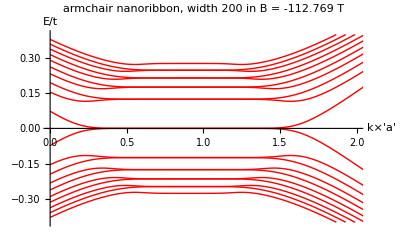

```mathematica
spectrumPlot[200,-field,Levels->-20,Type->"armchair",Ticks->Automatic,PlotRange->{{0,2},{-0.4,0.4}}]
```

Next, we fit the square root form.  The scaling appears robust for only the first 15 Landau levels, many fewer than in the zigzag case.  (One ought to keep in mind, though, that the LLs of the armchair nanoribbon have a higher degeneracy---compare the figures above.)

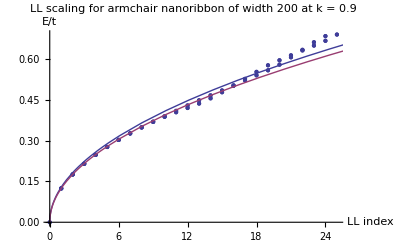
-Graphics--Graphics- | ML fit
-Graphics- | Inifite sheet result

```mathematica
landauScalingPlot[200,-field,0.9,Type->"armchair",FittedLevels->50]
```

```mathematica
landauScalingFit[200,-field,0.9,FittedLevels->50,Type->"armchair"]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.129078 | 0.000574588 | 224.645 | 7.03223×10^-136